## Functions

```mathematica
GlobalSimplifyTermsInLoop[S_]:=Module[{temp,mask,nterms,terms,idxterms,subsets,isolatedterms,zeroQ,exprTeX,n},
temp = ExpandAll[S][[Range[Length[ExpandAll@S]]]];
mask = Table[(FreeQ[i,xf]&&FreeQ[i,yf])&&FreeQ[i,zf]||(FreeQ[i,xi]&&FreeQ[i,yi]&&FreeQ[i,zi]),{i,List@@temp}];
nterms = Length@mask;
terms = Range[nterms];
idxterms = Pick[terms,mask];
subsets = Subsets[idxterms,{2}];
Do[
isolatedterms = temp[[set]];
zeroQ = isolatedterms/.{xi->xf,yi->yf,zi->zf};
If[zeroQ == 0,terms = DeleteCases[terms,Alternatives@@set]]
,{set,subsets}];
Factor[temp[[terms]]]]
```

## Derivations

```mathematica
TetrahedronTransform={
x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ
}
```

{x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
coordTransform[pt_List,transform_,var_:Automatic]:=Module[{v,f},v=If[var===Automatic,Variables[Level[transform,{-1}]],var];
f=Function@@{v,transform};
f@@pt]
```

```mathematica
coordTransform[{0,0,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{1,0,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{0,1,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{0,0,1},TetrahedronTransform,{ϵ, η, ζ}]
```

{x1,y1,z1}

{x2,y2,z2}

{x3,y3,z3}

{x4,y4,z4}

```mathematica
D[TetrahedronTransform,{{ϵ, η, ζ}}]//MatrixForm
```

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
TetrahedronTransformVar={
x->x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y->y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z->z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ
}
```

{x→x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y→y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z→z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
J = D[TetrahedronTransform,{{ϵ, η, ζ}}]
J//MatrixForm
```

{{-x1+x2,-x1+x3,-x1+x4},{-y1+y2,-y1+y3,-y1+y4},{-z1+z2,-z1+z3,-z1+z4}}

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
Simplify@Expand@Det[J]
```

-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)-x2 y1 z4+x1 y2 z4-x1 y3 z4+x2 y3 z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)

```mathematica
(x^2)/.TetrahedronTransformVar
```

(x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η)^2

```mathematica
Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

Inertia Tensor

### ∫x^2dm

```mathematica
IX2 = Simplify@Expand[Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

### ∫y^2dm

```mathematica
IY2 = Simplify@Expand[Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))

### ∫z^2dm

```mathematica
IZ2 = Simplify@Expand[Integrate[(z^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))

```mathematica
result =Table[{f,Simplify@Expand[Integrate[(f)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]},{f,{x^2,y^2,z^2, y z, x z, x y}}]
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
substitution = Flatten@Table[ToExpression[StringJoin[ToString[f], ToString[i]]]-> Subscript[f,i], {f,{x,y,z}}, {i,1,4}]
```

{x1→x_1,x2→x_2,x3→x_3,x4→x_4,y1→y_1,y2→y_2,y3→y_3,y4→y_4,z1→z_1,z2→z_2,z3→z_3,z4→z_4}

```mathematica
result/.substitution
```

{{x^2,1/12 (x_1^2+x_2^2+x_3^2+2 x_3 x_4+2 x_4^2+x_2 (x_3+2 x_4)-x_1 (x_2+x_3+2 x_4))},{y^2,1/12 (y_1^2+y_2^2+y_3^2+2 y_3 y_4+2 y_4^2+y_2 (y_3+2 y_4)-y_1 (y_2+y_3+2 y_4))},{z^3,1/120 (-4 z_1^3+6 z_2^3+6 z_3^3+15 z_3^2 z_4+20 z_3 z_4^2+15 z_4^3+3 z_2^2 (2 z_3+5 z_4)+z_1^2 (11 z_2+11 z_3+20 z_4)+z_2 (6 z_3^2+15 z_3 z_4+20 z_4^2)-z_1 (9 z_2^2+9 z_2 z_3+9 z_3^2+25 z_2 z_4+25 z_3 z_4+25 z_4^2))},{y z,1/24 (-y_3 z_1-2 y_4 z_1+y_3 z_2+2 y_4 z_2+2 y_3 z_3+2 y_4 z_3+y_1 (2 z_1-z_2-z_3-2 z_4)+2 y_3 z_4+4 y_4 z_4+y_2 (-z_1+2 z_2+z_3+2 z_4))},{x z,1/24 (-x_3 z_1-2 x_4 z_1+x_3 z_2+2 x_4 z_2+2 x_3 z_3+2 x_4 z_3+x_1 (2 z_1-z_2-z_3-2 z_4)+2 x_3 z_4+4 x_4 z_4+x_2 (-z_1+2 z_2+z_3+2 z_4))},{x y,1/24 (-x_3 y_1-2 x_4 y_1+x_3 y_2+2 x_4 y_2+2 x_3 y_3+2 x_4 y_3+x_1 (2 y_1-y_2-y_3-2 y_4)+2 x_3 y_4+4 x_4 y_4+x_2 (-y_1+2 y_2+y_3+2 y_4))}}

```mathematica
Table[expr[[2]]/.substitution, {expr, result}]
```

{1/12 (x_1^2+x_2^2+x_3^2+2 x_3 x_4+2 x_4^2+x_2 (x_3+2 x_4)-x_1 (x_2+x_3+2 x_4)),1/12 (y_1^2+y_2^2+y_3^2+2 y_3 y_4+2 y_4^2+y_2 (y_3+2 y_4)-y_1 (y_2+y_3+2 y_4)),1/120 (-4 z_1^3+6 z_2^3+6 z_3^3+15 z_3^2 z_4+20 z_3 z_4^2+15 z_4^3+3 z_2^2 (2 z_3+5 z_4)+z_1^2 (11 z_2+11 z_3+20 z_4)+z_2 (6 z_3^2+15 z_3 z_4+20 z_4^2)-z_1 (9 z_2^2+9 z_2 z_3+9 z_3^2+25 z_2 z_4+25 z_3 z_4+25 z_4^2)),1/24 (-y_3 z_1-2 y_4 z_1+y_3 z_2+2 y_4 z_2+2 y_3 z_3+2 y_4 z_3+y_1 (2 z_1-z_2-z_3-2 z_4)+2 y_3 z_4+4 y_4 z_4+y_2 (-z_1+2 z_2+z_3+2 z_4)),1/24 (-x_3 z_1-2 x_4 z_1+x_3 z_2+2 x_4 z_2+2 x_3 z_3+2 x_4 z_3+x_1 (2 z_1-z_2-z_3-2 z_4)+2 x_3 z_4+4 x_4 z_4+x_2 (-z_1+2 z_2+z_3+2 z_4)),1/24 (-x_3 y_1-2 x_4 y_1+x_3 y_2+2 x_4 y_2+2 x_3 y_3+2 x_4 y_3+x_1 (2 y_1-y_2-y_3-2 y_4)+2 x_3 y_4+4 x_4 y_4+x_2 (-y_1+2 y_2+y_3+2 y_4))}

```mathematica
result
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
Collect[result[[6,2]],{x1,x2,x3,x4}]
```

1/24 x1 (2 y1-y2-y3-2 y4)+1/24 x2 (-y1+2 y2+y3+2 y4)+1/24 x3 (-y1+y2+2 y3+2 y4)+1/24 x4 (-2 y1+2 y2+2 y3+4 y4)

```mathematica
Normal[CoefficientArrays[1/24 x1 (2 y1-y2-y3-2 y4)+1/24 x2 (-y1+2 y2+y3+2 y4)+1/24 x3 (-y1+y2+2 y3+2 y4)+1/24 x4 (-2 y1+2 y2+2 y3+4 y4),{x1,x2,x3,x4}]]
```

{0,{1/24 (2 y1-y2-y3-2 y4),1/24 (-y1+2 y2+y3+2 y4),1/24 (-y1+y2+2 y3+2 y4),1/24 (-2 y1+2 y2+2 y3+4 y4)}}

```mathematica
Last[%59]
```

SparseArray[…]

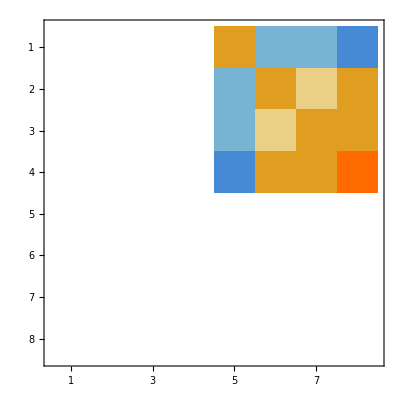

```mathematica
MatrixPlot[%60]
```

```mathematica
expandedExpr = Expand@result[[6,2]]
coeffMatrix=CoefficientArrays[expandedExpr,{x1,x2,x3,x4,y1,y2,y3,y4}][[3]]
MatrixForm[coeffMatrix]
```

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

SparseArray[…]

```mathematica
X = {x1,x2,x3,x4,y1,y2,y3,y4}
coeffMatrix=CoefficientArrays[expandedExpr,X][[3]]
coefs = Normal[coeffMatrix]
Expand[X . coefs .Xᵀ]
```

{x1,x2,x3,x4,y1,y2,y3,y4}

SparseArray[…]

{{0,0,0,0,1/12,-1/24,-1/24,-1/12},{0,0,0,0,-1/24,1/12,1/24,1/12},{0,0,0,0,-1/24,1/24,1/12,1/12},{0,0,0,0,-1/12,1/12,1/12,1/6},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

```mathematica
Normal[CoefficientArrays[%78,{y1,y2,y3,y4}]]
```

{{y1/12-y2/24-y3/24-y4/12,-y1/24+y2/12+y3/24+y4/12,-y1/24+y2/24+y3/12+y4/12,-y1/12+y2/12+y3/12+y4/6}}

```mathematica
result
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
result[[1]]
```

{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))}

```mathematica
X={x1,x2,x3,x4};
Y={y1,y2,y3,y4};
Z = {z1,z2,z3,z4};


xxcoeffMatrix=Table[Coefficient[Coefficient[result[[1,2]]*12,X[[i]]],X[[j]]],{i,1,4},{j,1,4}]

yzcoeffMatrix=Table[Coefficient[Coefficient[result[[4,2]]*24,Y[[i]]],Z[[j]]],{i,1,4},{j,1,4}];
xzcoeffMatrix=Table[Coefficient[Coefficient[result[[5,2]]*24,X[[i]]],Z[[j]]],{i,1,4},{j,1,4}];
xycoeffMatrix=Table[Coefficient[Coefficient[result[[6,2]]*24,X[[i]]],Y[[j]]],{i,1,4},{j,1,4}];

yzcoeffMatrix//MatrixForm
 xzcoeffMatrix//MatrixForm
xycoeffMatrix//MatrixForm
```

{{0,-1,-1,-2},{-1,0,1,2},{-1,1,0,2},{-2,2,2,0}}

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

```mathematica
i^2
```

i^2

{{1,-1,-1,-2},{0,1,1,2},{0,0,1,2},{0,0,0,2}}

```mathematica
xxcoeffMatrix = Normal[CoefficientArrays[result[[1,2]]*12,X][[3]]]
Expand[(1/12) X.xxcoeffMatrix.Xᵀ]
 Expand[result[[1,2]]]
```

{{1,-1,-1,-2},{0,1,1,2},{0,0,1,2},{0,0,0,2}}

x1^2/12-(x1 x2)/12+x2^2/12-(x1 x3)/12+(x2 x3)/12+x3^2/12-(x1 x4)/6+(x2 x4)/6+(x3 x4)/6+x4^2/6

x1^2/12-(x1 x2)/12+x2^2/12-(x1 x3)/12+(x2 x3)/12+x3^2/12-(x1 x4)/6+(x2 x4)/6+(x3 x4)/6+x4^2/6

```mathematica
Expand[X . coeffMatrix.Yᵀ]
```

2 x1 y1-x2 y1-x3 y1-2 x4 y1-x1 y2+2 x2 y2+x3 y2+2 x4 y2-x1 y3+x2 y3+2 x3 y3+2 x4 y3-2 x1 y4+2 x2 y4+2 x3 y4+4 x4 y4

```mathematica
expandedExpr
```

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

```mathematica
coeffMatrix//MatrixForm
```

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

```mathematica
Mesh
```

```mathematica
eq1 =c == v1 + λ q
eq2 =c == v2 + ϕ s

expr = {q -> v2 + (v3-v2)/2 -v1
,s ->v3-v2 + (v1 - v3)/2}
eq1/.expr
eq2/.expr
```

c==v1+q λ

c==v2+s ϕ

{q→-v1+v2+1/2 (-v2+v3),s→-v2+(v1-v3)/2+v3}

c==v1+(-v1+v2+1/2 (-v2+v3)) λ

c==v2+(-v2+(v1-v3)/2+v3) ϕ

```mathematica
Coefficient[(v1 + λ q)/.expr, {v1,v2,v3}]
Coefficient[(v2 + ϕ s)/.expr, {v1,v2,v3}]
```

{1-λ,λ/2,λ/2}

{ϕ/2,1-ϕ,ϕ/2}

```mathematica
Expand[q/.expr]*2/3 + v1
```

v1+2/3 (-v1+v2/2+v3/2)

```mathematica
Simplify[v1+2/3 (-v1+v2/2+v3/2)]
```

1/3 (v1+v2+v3)

```mathematica
eq1/.expr
```

c==v1+(-v1+v2+1/2 (-v2+v3)) λ

```mathematica
eq2/.expr
```

c==v2+(-v2+(v1-v3)/2+v3) ϕ

```mathematica
r = Solve[{c==v2+(-v2+(v1-v3)/2+v3) ϕ, c==v1+(-v1+v2+1/2 (-v2+v3)) λ}, {λ,ϕ}]//Flatten
```

{λ→-(2 (c-v1))/(2 v1-v2-v3),ϕ→-(2 (c-v2))/(-v1+2 v2-v3)}

```mathematica
Solve[,]
```

{{}}

```mathematica
eq1/.expr/.r
```

c==v1-(2 (c-v1) (-v1+v2+1/2 (-v2+v3)))/(2 v1-v2-v3)

```mathematica
Solve[c==v1-(2 (c-v1) (-v1+v2+1/2 (-v2+v3)))/(2 v1-v2-v3),c]
```

{{}}

```mathematica
r = {x,y,z}
n = {u,v,w}
Simplify[1/2 Curl[n×r,{x,y,z}].n]
```

{x,y,z}

{u,v,w}

u^2+v^2+w^2

{w y-v z,-w x+u z,v x-u y}

```mathematica
rcurve = {x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
r = {x,y,z}
n = {nx,ny,nz}
dr = D[r/.rcurve, t]
F = 1/2(n×(r/.rcurve))
Collect[Simplify@Integrate[F.dr,{t,0,1}],n]
```

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{1/2 (-nz t yf-nz yi+nz t yi+ny t zf+ny zi-ny t zi),1/2 (nz t xf+nz xi-nz t xi-nx t zf-nx zi+nx t zi),1/2 (-ny t xf-ny xi+ny t xi+nx t yf+nx yi-nx t yi)}

1/2 nz (xi yf-xf yi)+1/2 ny (-xi zf+xf zi)+1/2 nx (yi zf-yf zi)

```mathematica
res = Simplify[Integrate[F.dr,{t,0,1}]]
```

1/2 (nz xi yf-nz xf yi-ny xi zf+nx yi zf+ny xf zi-nx yf zi)

```mathematica
Normal[CoefficientArrays[res*2, n]]
```

{0,{yi zf-yf zi,-xi zf+xf zi,xi yf-xf yi}}

```mathematica
SimplifyTermsInLoop[xi yf-xf yi]
```

Factored Expression

xi yf-xf yi

Expanded Expression

xi yf-xf yi

Reduced Expression (trailing-leading term cancelations)

xi yf-xf yi

TeXForm Reduced Expression

-x_(1+i) y_i+x_i y_(1+i)

x_i y_{i+1}-x_{i+1} y_i

xi yf-xf yi

```mathematica
F.dr
```

1/2 (-ny t xf-ny xi+ny t xi+nx t yf+nx yi-nx t yi) (zf-zi)+1/2 (yf-yi) (nz t xf+nz xi-nz t xi-nx t zf-nx zi+nx t zi)+1/2 (xf-xi) (-nz t yf-nz yi+nz t yi+ny t zf+ny zi-ny t zi)

```mathematica
Expand[1/2 (-ny t xf-ny xi+ny t xi+nx t yf+nx yi-nx t yi) (zf-zi)+1/2 (yf-yi) (nz t xf+nz xi-nz t xi-nx t zf-nx zi+nx t zi)+1/2 (xf-xi) (-nz t yf-nz yi+nz t yi+ny t zf+ny zi-ny t zi)]
```

(nz xi yf)/2-(nz xf yi)/2-(ny xi zf)/2+(nx yi zf)/2+(ny xf zi)/2-(nx yf zi)/2

```mathematica
idx = Table[{ToExpression[StringJoin[ToString[var],"i"]]->Subscript[var, i], ToExpression[StringJoin[ToString[var],"f"]]->Subscript[var, i+1]}, {var,{x,y,z}}]//Flatten
```

{xi→x_i,xf→x_(1+i),yi→y_i,yf→y_(1+i),zi→z_i,zf→z_(1+i)}

```mathematica
ri = {xi,yi,zi}
rf = {xf,yf,zf}

(ri ×rf).n/2
```

{xi,yi,zi}

{xf,yf,zf}

1/2 (nz (xi yf-xf yi)+ny (-xi zf+xf zi)+nx (yi zf-yf zi))

```mathematica
FullSimplify[res == (ri ×rf).n/2]
```

True

```mathematica
r = {x,y,z}
F =x^2  n×r
n
```

{x,y,z}

{x^2 (-nz y+ny z),x^2 (nz x-nx z),x^2 (-ny x+nx y)}

{nx,ny,nz}

```mathematica
Curl[F×n,{x,y,z}].n
```

ny (2 nx nz x^2+2 ny nz x y-2 nx^2 x z-2 ny^2 x z)+nz (-2 nx ny x^2+2 nx^2 x y+2 nz^2 x y-2 ny nz x z)

```mathematica
Curl[F×n,{x,y,z}]
```

{0,2 nx nz x^2+2 ny nz x y-2 nx^2 x z-2 ny^2 x z,-2 nx ny x^2+2 nx^2 x y+2 nz^2 x y-2 ny nz x z}

```mathematica
Curl[ f[x]n×r, {x,y,z}]
```

{2 nx f[x],2 ny f[x]-(-ny x+nx y) f'[x],2 nz f[x]+(nz x-nx z) f'[x]}

```mathematica
{2 f[x],2 f[x]-(- x+(nx/ny) y) f'[x],2 f[x]+( x-(nx/nz) z) f'[x]}.n
```

2 nx f[x]+ny (2 f[x]-(-x+(nx y)/ny) f'[x])+nz (2 f[x]+(x-(nx z)/nz) f'[x])

```mathematica
Simplify[2 nx f[x]+ny (2 f[x]-(-x+(nx y)/ny) f'[x])+nz (2 f[x]+(x-(nx z)/nz) f'[x])]
```

2 (nx+ny+nz) f[x]+(ny x+nz x-nx (y+z)) f'[x]

```mathematica
Curl[n×(r+{0,x^2,0}), {x,y,z}]
```

{2 nx,2 ny-2 nx x,2 nz}

```mathematica
Curl[{ 0,x^2/(2*nz),0}, {x,y,z}].n
```

x

```mathematica
Curl[{ F1[x,z]*ny,F2[x,y]*nz,F3[y,z]*nx}, {x,y,z}]
Curl[{ F1[x,z]*ny,F2[x,y]*nz,F3[y,z]*nx}, {x,y,z}].n
```

{nx F3^(1,0)[y,z],ny F1^(0,1)[x,z],nz F2^(1,0)[x,y]}

ny^2 F1^(0,1)[x,z]+nz^2 F2^(1,0)[x,y]+nx^2 F3^(1,0)[y,z]

```mathematica
F = {x z * ny - x y * nz, 0 , 0};
Simplify[Expand[Curl[F, {x,y,z}].n]]
F = {0, x^2 * nz-+  z * nx, 0};
Simplify[Expand[Curl[F, {x,y,z}].n]]
F = {0, 0 ,- x^2  *ny + y*nx };
Simplify[Expand[Curl[F, {x,y,z}].n]]

F ={x z / ny - x y / nz, x^2 / nz +  z / nx ,x^2  /ny + y/nx};
F ={x z * ny - x y * nz, 0 , 0} + {0, x^2 * nz-+  z * nx, 0} + {0, 0 ,- x^2  *ny + y*nx }
Expand[Curl[F, {x,y,z}]]
Simplify[Expand[Curl[F, {x,y,z}].n]]
```

(ny^2+nz^2) x

nx^2+2 nz^2 x

nx^2+2 ny^2 x

{-nz x y+ny x z,nz x^2-nx z,-ny x^2+nx y}

{2 nx,3 ny x,3 nz x}

2 nx^2+3 (ny^2+nz^2) x

```mathematica
F1 =2 {x z * ny - x y * nz, 0 , 0};
Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0, x^2 * (nz + nx^2/nz) , 0};
Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,- x^2  *(ny +nx^2/ny) };
Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)/4
Simplify[Expand[Curl[F, {x,y,z}].n]]

parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
expr = Integrate[Ft.dr,{t,0,1}]
ce = Collect[expr,{nx,ny,nz}]
```

2 (ny^2+nz^2) x

2 (nx^2+nz^2) x

2 (nx^2+ny^2) x

{1/2 (-nz x y+ny x z),1/4 (nx^2/nz+nz) x^2,-1/4 (nx^2/ny+ny) x^2}

(nx^2+ny^2+nz^2) x

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{1/2 (-nz (t (xf-xi)+xi) (t (yf-yi)+yi)+ny (t (xf-xi)+xi) (t (zf-zi)+zi)),1/4 (nx^2/nz+nz) (t (xf-xi)+xi)^2,-1/4 (nx^2/ny+ny) (t (xf-xi)+xi)^2}

(nx^2 (xf^2+xf xi+xi^2) (ny (yf-yi)+nz (-zf+zi))+ny nz (nz (2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi))+ny (2 xf xi (-zf+zi)-xi^2 (2 zf+zi)+xf^2 (zf+2 zi))))/(12 ny nz)

1/12 nz (2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi))+nx^2 (((xf^2+xf xi+xi^2) (yf-yi))/(12 nz)+((xf^2+xf xi+xi^2) (-zf+zi))/(12 ny))+1/12 ny (2 xf xi (-zf+zi)-xi^2 (2 zf+zi)+xf^2 (zf+2 zi))

```mathematica
minr = 1/12 nz SimplifyTermsInLoop[(2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi))] + nx^2 (SimplifyTermsInLoop[(xf^2+xf xi+xi^2) (yf-yi)]/(12 nz)+SimplifyTermsInLoopxz[(xf^2+xf xi+xi^2) (-zf+zi)]/(12 ny))+1/12 ny SimplifyTermsInLoopxz[(2 xf xi (-zf+zi)-xi^2 (2 zf+zi)+xf^2 (zf+2 zi))]
```

Factored Expression

2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi)

Expanded Expression

-xf^2 yf+2 xf xi yf+2 xi^2 yf-2 xf^2 yi-2 xf xi yi+xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-2 (xf+xi) (-xi yf+xf yi)

TeXForm Reduced Expression

-2 (x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i))

-2 \left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)

Factored Expression

(xf^2+xf xi+xi^2) (yf-yi)

Expanded Expression

xf^2 yf+xf xi yf+xi^2 yf-xf^2 yi-xf xi yi-xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-((xf+xi) (-xi yf+xf yi))

TeXForm Reduced Expression

-((x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i)))

-\left(\left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)\right)

Factored Expression

-((xf^2+xf xi+xi^2) (zf-zi))

Expanded Expression

-xf^2 zf-xf xi zf-xi^2 zf+xf^2 zi+xf xi zi+xi^2 zi

Reduced Expression (trailing-leading term cancelations)

(xf+xi) (-xi zf+xf zi)

TeXForm Reduced Expression

(x_i+x_(1+i)) (x_(1+i) z_i-x_i z_(1+i))

\left(x_i+x_{i+1}\right) \left(x_{i+1} z_i-x_i z_{i+1}\right)

Factored Expression

2 xf xi (-zf+zi)-xi^2 (2 zf+zi)+xf^2 (zf+2 zi)

Expanded Expression

xf^2 zf-2 xf xi zf-2 xi^2 zf+2 xf^2 zi+2 xf xi zi-xi^2 zi

Reduced Expression (trailing-leading term cancelations)

2 (xf+xi) (-xi zf+xf zi)

TeXForm Reduced Expression

2 (x_i+x_(1+i)) (x_(1+i) z_i-x_i z_(1+i))

2 \left(x_i+x_{i+1}\right) \left(x_{i+1} z_i-x_i z_{i+1}\right)

-1/6 nz (xf+xi) (-xi yf+xf yi)+1/6 ny (xf+xi) (-xi zf+xf zi)+nx^2 (-((xf+xi) (-xi yf+xf yi))/(12 nz)+((xf+xi) (-xi zf+xf zi))/(12 ny))

```mathematica
minr /.{nx ->1,}
```

-1/6 nz (xf+xi) (-xi yf+xf yi)+1/6 ny (xf+xi) (-xi zf+xf zi)

```mathematica
Curl[{-x^2/(2*nz),0,0},{x,y,z}]
```

{0,0,0}

```mathematica
Curl[{ F1[x,y,z]*ny,F2[x,y,z]*nz,F3[x,y,z]*nx}, {x,y,z}]//MatrixForm
```

(-nz F2^(0,0,1)[x,y,z]+nx F3^(0,1,0)[x,y,z]
ny F1^(0,0,1)[x,y,z]-nx F3^(1,0,0)[x,y,z]
-ny F1^(0,1,0)[x,y,z]+nz F2^(1,0,0)[x,y,z])

```mathematica
Expand[Curl[F, {x,y,z}]].n
```

ny^2 x+nz ((nx^2 x)/nz+nz x)

## Centroid x_c

```mathematica
parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
F = {x z ny,(nz+nx^2/nz) x^2 /2 ,0};
Simplify[Expand[Curl[F, {x,y,z}].n]]
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
Integrate[Ft.dr,{t,0,1}]
```

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

(nx^2+ny^2+nz^2) x

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{ny (t (xf-xi)+xi) (t (zf-zi)+zi),1/2 (nx^2/nz+nz) (t (xf-xi)+xi)^2,0}

1/6 ((nx^2/nz+nz) (xf^2+xf xi+xi^2) (yf-yi)+ny (xf-xi) (xf (2 zf+zi)+xi (zf+2 zi)))

```mathematica
1/6 ((nx^2/nz+nz) SimplifyTermsInLoop[(xf^2+xf xi+xi^2) (yf-yi)]+ny SimplifyTermsInLoopxz[(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))])
```

Factored Expression

(xf^2+xf xi+xi^2) (yf-yi)

Expanded Expression

xf^2 yf+xf xi yf+xi^2 yf-xf^2 yi-xf xi yi-xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-((xf+xi) (-xi yf+xf yi))

TeXForm Reduced Expression

-((x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i)))

-\left(\left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)\right)

Factored Expression

(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))

Expanded Expression

2 xf^2 zf-xf xi zf-xi^2 zf+xf^2 zi+xf xi zi-2 xi^2 zi

Reduced Expression (trailing-leading term cancelations)

(xf+xi) (-xi zf+xf zi)

TeXForm Reduced Expression

(x_i+x_(1+i)) (x_(1+i) z_i-x_i z_(1+i))

\left(x_i+x_{i+1}\right) \left(x_{i+1} z_i-x_i z_{i+1}\right)

1/6 (-((nx^2/nz+nz) (xf+xi) (-xi yf+xf yi))+ny (xf+xi) (-xi zf+xf zi))

## Centroid y

```mathematica
parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
F = {x z ny,(nz+nx^2/nz) x^2 /2 ,0};
F = {0,x y nz ,(nx+ny^2/nx) y^2 /2};
Simplify[Expand[Curl[F, {x,y,z}].n]]
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
Integrate[Ft.dr,{t,0,1}]
```

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

(nx^2+ny^2+nz^2) y

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{0,nz (t (xf-xi)+xi) (t (yf-yi)+yi),1/2 (nx+ny^2/nx) (t (yf-yi)+yi)^2}

1/6 (nz (yf-yi) (xf (2 yf+yi)+xi (yf+2 yi))+(nx+ny^2/nx) (yf^2+yf yi+yi^2) (zf-zi))

```mathematica
1/6 (nz SimplifyTermsInLoop[(yf-yi) (xf (2 yf+yi)+xi (yf+2 yi))]+(nx+ny^2/nx) SimplifyTermsInLoopyz[(yf^2+yf yi+yi^2) (zf-zi)])
```

Factored Expression

(yf-yi) (xf (2 yf+yi)+xi (yf+2 yi))

Expanded Expression

2 xf yf^2+xi yf^2-xf yf yi+xi yf yi-xf yi^2-2 xi yi^2

Reduced Expression (trailing-leading term cancelations)

(yf+yi) (xi yf-xf yi)

TeXForm Reduced Expression

(y_i+y_(1+i)) (-x_(1+i) y_i+x_i y_(1+i))

\left(y_i+y_{i+1}\right) \left(x_i y_{i+1}-x_{i+1} y_i\right)

Factored Expression

(yf^2+yf yi+yi^2) (zf-zi)

Expanded Expression

yf^2 zf+yf yi zf+yi^2 zf-yf^2 zi-yf yi zi-yi^2 zi

Reduced Expression (trailing-leading term cancelations)

-((yf+yi) (-yi zf+yf zi))

TeXForm Reduced Expression

-((y_i+y_(1+i)) (y_(1+i) z_i-y_i z_(1+i)))

-\left(\left(y_i+y_{i+1}\right) \left(y_{i+1} z_i-y_i z_{i+1}\right)\right)

```mathematica
ToPython[1/6 (nz (yf+yi) (xi yf-xf yi)-(nx+ny^2/nx) (yf+yi) (-yi zf+yf zi))]
```

aux0=(nz*((yf+yi)*((xi*yf)-(xf*yi))))-((nx+((ny**2)/nx))*((yf+yi)*((yf*zi)-(yi*zf))));
output=(1./6.)*aux0;

## Centroid z

```mathematica
parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
F = {x z ny,(nz+nx^2/nz) x^2 /2 ,0};
F = {0,x y nz ,(nx+ny^2/nx) y^2 /2};
F = {(ny+nz^2/ny) z^2 /2,0 ,y z nx};
Simplify[Expand[Curl[F, {x,y,z}].n]]
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
Integrate[Ft.dr,{t,0,1}]
```

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

(nx^2+ny^2+nz^2) z

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{1/2 (ny+nz^2/ny) (t (zf-zi)+zi)^2,0,nx (t (yf-yi)+yi) (t (zf-zi)+zi)}

1/6 ((ny+nz^2/ny) (xf-xi) (zf^2+zf zi+zi^2)+nx (zf-zi) (yf (2 zf+zi)+yi (zf+2 zi)))

```mathematica
1/6 ((ny+nz^2/ny) SimplifyTermsInLoopxz[(xf-xi) (zf^2+zf zi+zi^2)]+nx SimplifyTermsInLoopyz[(zf-zi) (yf (2 zf+zi)+yi (zf+2 zi))])
```

Factored Expression

(xf-xi) (zf^2+zf zi+zi^2)

Expanded Expression

xf zf^2-xi zf^2+xf zf zi-xi zf zi+xf zi^2-xi zi^2

Reduced Expression (trailing-leading term cancelations)

-((zf+zi) (xi zf-xf zi))

TeXForm Reduced Expression

-((z_i+z_(1+i)) (-x_(1+i) z_i+x_i z_(1+i)))

-\left(\left(z_i+z_{i+1}\right) \left(x_i z_{i+1}-x_{i+1} z_i\right)\right)

Factored Expression

(zf-zi) (yf (2 zf+zi)+yi (zf+2 zi))

Expanded Expression

2 yf zf^2+yi zf^2-yf zf zi+yi zf zi-yf zi^2-2 yi zi^2

Reduced Expression (trailing-leading term cancelations)

(zf+zi) (yi zf-yf zi)

TeXForm Reduced Expression

(z_i+z_(1+i)) (-y_(1+i) z_i+y_i z_(1+i))

\left(z_i+z_{i+1}\right) \left(y_i z_{i+1}-y_{i+1} z_i\right)

```mathematica
ToPython[1/6 (-((ny+nz^2/ny) (zf+zi) (xi zf-xf zi))+nx (zf+zi) (yi zf-yf zi))]
```

aux0=(nx*((zf+zi)*((yi*zf)-(yf*zi))))-((ny+((nz**2)/ny))*((zf+zi)*((xi*zf)-(xf*zi))));
output=(1./6.)*aux0;

```mathematica
SimplifyTermsInLoopxz[S_]:=Module[{temp,mask,nterms,terms,idxterms,subsets,isolatedterms,zeroQ,exprTeX,n},
temp = ExpandAll[S][[Range[Length[ExpandAll@S]]]];
mask = Table[(FreeQ[i,xf]&&FreeQ[i,zf])||(FreeQ[i,xi]&&FreeQ[i,zi]),{i,List@@temp}];
nterms = Length@mask;
terms = Range[nterms];
idxterms = Pick[terms,mask];
subsets = Subsets[idxterms,{2}];
Do[
isolatedterms = temp[[set]];
zeroQ = isolatedterms/.{xi->xf,zi->zf};
If[zeroQ == 0,terms = DeleteCases[terms,Alternatives@@set]]
,{set,subsets}];

Print[style1@"Factored Expression"];
Print[Simplify[temp]];

Print[style1@"Expanded Expression"];
Print[temp];
Print[style1@"Reduced Expression (trailing-leading term cancelations)"];
Print[Factor[temp[[terms]]]];
Print[style1@"TeXForm Reduced Expression"];
exprTeX = Simplify[Factor[Expand[temp[[terms]]]]]/.{xf ->Subscript[ x,i+1],xi-> Subscript[x,i],zf ->Subscript[ z,i+1],zi->Subscript[ z,i]};
Print[exprTeX];
Print[TeXForm[exprTeX]];
Factor[temp[[terms]]]]

SimplifyTermsInLoopyz[S_]:=Module[{temp,mask,nterms,terms,idxterms,subsets,isolatedterms,zeroQ,exprTeX,n},
temp = ExpandAll[S][[Range[Length[ExpandAll@S]]]];
mask = Table[(FreeQ[i,yf]&&FreeQ[i,zf])||(FreeQ[i,yi]&&FreeQ[i,zi]),{i,List@@temp}];
nterms = Length@mask;
terms = Range[nterms];
idxterms = Pick[terms,mask];
subsets = Subsets[idxterms,{2}];
Do[
isolatedterms = temp[[set]];
zeroQ = isolatedterms/.{yi->yf,zi->zf};
If[zeroQ == 0,terms = DeleteCases[terms,Alternatives@@set]]
,{set,subsets}];

Print[style1@"Factored Expression"];
Print[Simplify[temp]];

Print[style1@"Expanded Expression"];
Print[temp];
Print[style1@"Reduced Expression (trailing-leading term cancelations)"];
Print[Factor[temp[[terms]]]];
Print[style1@"TeXForm Reduced Expression"];
exprTeX = Simplify[Factor[Expand[temp[[terms]]]]]/.{yf ->Subscript[ y,i+1],yi-> Subscript[y,i],zf ->Subscript[ z,i+1],zi->Subscript[ z,i]};
Print[exprTeX];
Print[TeXForm[exprTeX]];
Factor[temp[[terms]]]]

SimplifyTermsInLoopxz[(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))]
```

Factored Expression

(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))

Expanded Expression

2 xf^2 zf-xf xi zf-xi^2 zf+xf^2 zi+xf xi zi-2 xi^2 zi

Reduced Expression (trailing-leading term cancelations)

(xf+xi) (-xi zf+xf zi)

TeXForm Reduced Expression

(x_i+x_(1+i)) (x_(1+i) z_i-x_i z_(1+i))

\left(x_i+x_{i+1}\right) \left(x_{i+1} z_i-x_i z_{i+1}\right)

(xf+xi) (-xi zf+xf zi)

```mathematica
S = (xf-xi) (2 xf zf+xi zf+xf zi+2 xi zi);
temp = ExpandAll[S][[Range[Length[ExpandAll@S]]]];
mask = Table[(FreeQ[i,xf]&&FreeQ[i,zf])||(FreeQ[i,xi]&&FreeQ[i,zi]),{i,List@@temp}]
nterms = Length@mask
terms = Range[nterms]
idxterms = Pick[terms,mask]
subsets = Subsets[idxterms,{2}]
```

{True,False,False,False,False,True}

6

{1,2,3,4,5,6}

{1,6}

{{1,6}}

```mathematica
List@@temp
```

{2 xf^2 zf,-xf xi zf,-xi^2 zf,xf^2 zi,xf xi zi,-2 xi^2 zi}

```mathematica
FreeQ[-xf xi zf,xf]
FreeQ[2 xf^2 zf,xf]
```

False

False

```mathematica
F = {x z ny ,1/2 (nz+nx^2/nz)x^2 , 0};
Simplify[Expand[Curl[F, {x,y,z}].n]]

parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
expr = Integrate[Ft.dr,{t,0,1}]
ce = Collect[expr,{nx,ny,nz}]
```

(nx^2+ny^2+nz^2) x

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{ny (t (xf-xi)+xi) (t (zf-zi)+zi),1/2 (nx^2/nz+nz) (t (xf-xi)+xi)^2,0}

1/6 ((nx^2/nz+nz) (xf^2+xf xi+xi^2) (yf-yi)+ny (xf-xi) (xf (2 zf+zi)+xi (zf+2 zi)))

(nx^2 (xf^2+xf xi+xi^2) (yf-yi))/(6 nz)+1/6 nz (xf^2+xf xi+xi^2) (yf-yi)+1/6 ny (xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))

```mathematica
1/6 nx SimplifyTermsInLoop[(xf^2+xf xi+xi^2) (yf-yi)]+1/6 nz SimplifyTermsInLoop[(xf^2+xf xi+xi^2) (yf-yi)]+1/6 ny SimplifyTermsInLoopxz[(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))]
```

Factored Expression

(xf^2+xf xi+xi^2) (yf-yi)

Expanded Expression

xf^2 yf+xf xi yf+xi^2 yf-xf^2 yi-xf xi yi-xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-((xf+xi) (-xi yf+xf yi))

TeXForm Reduced Expression

-((x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i)))

-\left(\left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)\right)

Factored Expression

(xf^2+xf xi+xi^2) (yf-yi)

Expanded Expression

xf^2 yf+xf xi yf+xi^2 yf-xf^2 yi-xf xi yi-xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-((xf+xi) (-xi yf+xf yi))

TeXForm Reduced Expression

-((x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i)))

-\left(\left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)\right)

Factored Expression

(xf-xi) (xf (2 zf+zi)+xi (zf+2 zi))

Expanded Expression

2 xf^2 zf-xf xi zf-xi^2 zf+xf^2 zi+xf xi zi-2 xi^2 zi

Reduced Expression (trailing-leading term cancelations)

(xf+xi) (-xi zf+xf zi)

TeXForm Reduced Expression

(x_i+x_(1+i)) (x_(1+i) z_i-x_i z_(1+i))

\left(x_i+x_{i+1}\right) \left(x_{i+1} z_i-x_i z_{i+1}\right)

-1/6 nx (xf+xi) (-xi yf+xf yi)-1/6 nz (xf+xi) (-xi yf+xf yi)+1/6 ny (xf+xi) (-xi zf+xf zi)

```mathematica
F1 =2 {x z * ny - x y * nz, 0 , 0};
F1 = { z y , 0 , 0};
Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0, x^2 * (nz + nx^2/nz) , 0};
F2 = {0, x z , 0};
Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,- x^2  *(ny +nx^2/ny) };
F3 = {0, 0 ,y x };
Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)
Simplify[Expand[Curl[F, {x,y,z}].n]]
```

ny y-nz z

-nx x+nz z

nx x-ny y

{y z,x z,x y}

0

```mathematica
F1 =2 {x z * ny - x y * nz, 0 , 0};
F1 = { 0 , 0 , 0};
Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0, x^2 * (nz + nx^2/nz) , 0};
F2 = {0, x^2 /nz  , 0};
Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,- x^2  *(ny +nx^2/ny) };
F3 = {0, 0 ,-x^2 /ny};
Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)/4
Simplify[Expand[Curl[F, {x,y,z}].n]]

(*parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
expr = Integrate[Ft.dr,{t,0,1}]
ce = Collect[expr,{nx,ny,nz}]*)
```

0

2 x

2 x

{0,x^2/(4 nz),-x^2/(4 ny)}

x

```mathematica
F1 = { z^2 *ny  + nz*y, 0 , 0};
Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0,-nx z^2/2 + nz * x , 0};
Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,z y*nx};
Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)/2
Simplify[Expand[Curl[F, {x,y,z}].n]]
parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)}
r= {x,y,z}
n = {nx,ny,nz}
dr = D[r/.parameterization, t]
Ft = F/.parameterization
expr = Integrate[Ft.dr,{t,0,1}]
ce = Collect[expr,{nx,ny,nz}]
```

-nz^2+2 ny^2 z

nz^2+nx^2 z

nx^2 z

{1/2 (nz y+ny z^2),1/2 (nz x-(nx z^2)/2),(nx y z)/2}

(nx^2+ny^2) z

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi}

{x,y,z}

{nx,ny,nz}

{xf-xi,yf-yi,zf-zi}

{1/2 (nz (t (yf-yi)+yi)+ny (t (zf-zi)+zi)^2),1/2 (nz (t (xf-xi)+xi)-1/2 nx (t (zf-zi)+zi)^2),1/2 nx (t (yf-yi)+yi) (t (zf-zi)+zi)}

(nz xf yf)/2-(nz xi yi)/2+1/6 ny xf zf^2-1/6 ny xi zf^2+1/12 nx yf zf^2+1/6 nx yi zf^2+1/6 ny xf zf zi-1/6 ny xi zf zi-1/6 nx yf zf zi+1/6 nx yi zf zi+1/6 ny xf zi^2-1/6 ny xi zi^2-1/6 nx yf zi^2-1/12 nx yi zi^2

nz ((xf yf)/2-(xi yi)/2)+ny ((xf zf^2)/6-(xi zf^2)/6+(xf zf zi)/6-(xi zf zi)/6+(xf zi^2)/6-(xi zi^2)/6)+nx ((yf zf^2)/12+(yi zf^2)/6-(yf zf zi)/6+(yi zf zi)/6-(yf zi^2)/6-(yi zi^2)/12)

```mathematica
nz ((xf yf)/2-(xi yi)/2)+ny ((xf zf^2)/6-(xi zf^2)/6+(xf zf zi)/6-(xi zf zi)/6+(xf zi^2)/6-(xi zi^2)/6)+nx ((yf zf^2)/12+(yi zf^2)/6-(yf zf zi)/6+(yi zf zi)/6-(yf zi^2)/6-(yi zi^2)/12)
```

nz ((xf yf)/2-(xi yi)/2)+ny ((xf zf^2)/6-(xi zf^2)/6+(xf zf zi)/6-(xi zf zi)/6+(xf zi^2)/6-(xi zi^2)/6)+nx ((yf zf^2)/12+(yi zf^2)/6-(yf zf zi)/6+(yi zf zi)/6-(yf zi^2)/6-(yi zi^2)/12)

## Centroid Derivation

```mathematica
IntegrateLineExpression[F_]:=Module[{parameterization,r,dr,Ft,expr,n, t},
(*Clear variables to ensure they are symbolic and unassigned*)
Clear[nx,ny,nz,x,y,z,xi,xf,yi,yf,zi,zf];
parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)};
r= {x,y,z};
n = {nx,ny,nz};
dr = D[r/.parameterization, t];
Ft = F/.parameterization;
expr = Integrate[Ft.dr,{t,0,1}];
Print[expr];
Collect[GlobalSimplifyTermsInLoop[expr],n]]
```

### Centroid X

```mathematica
F1 = {0, 0 , 0};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0,nz x^2/2-ny y z  , 0};
Expand@Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,-ny x^2/2+nx x y };
Expand@Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)
Expand@Simplify[Expand[Curl[F, {x,y,z}].n]]

IntegrateLineExpression[F]
```

0

nz^2 x+nx ny y

nx^2 x+ny^2 x-nx ny y

{0,(nz x^2)/2-ny y z,-(ny x^2)/2+nx x y}

nx^2 x+ny^2 x+nz^2 x

-1/6 (ny (xf^2+xf xi+xi^2)-nx (xf (2 yf+yi)+xi (yf+2 yi))) (zf-zi)-1/6 (yf-yi) (-nz (xf^2+xf xi+xi^2)+ny yf (2 zf+zi)+ny yi (zf+2 zi))

1/6 nz (xf xi yf+xi^2 yf-xf^2 yi-xf xi yi)+1/6 nx (xi yf zf+xf yi zf+2 xi yi zf-2 xf yf zi-xi yf zi-xf yi zi)+1/6 ny (-xf xi zf-xi^2 zf+yf yi zf+yi^2 zf+xf^2 zi+xf xi zi-yf^2 zi-yf yi zi)

```mathematica
IntegrateLineExpression[{0,nz x^2/2  , 0}]
IntegrateLineExpression[{0,0  ,-ny x^2/2}]
IntegrateLineExpression[{0,0 ,nx x y}]
IntegrateLineExpression[{0,-ny y z ,0}]
```

-1/6 nz (xf+xi) (-xi yf+xf yi)

1/6 ny (xf+xi) (-xi zf+xf zi)

1/6 nx (xi yf zf+xf yi zf+2 xi yi zf-2 xf yf zi-xi yf zi-xf yi zi)

-1/6 ny (yf+yi) (-yi zf+yf zi)

```mathematica
F = {0,0 ,nx x y};
r= {x,y,z};
n = {nx,ny,nz};
dr = D[r/.parameterization, t];
Ft = F/.parameterization;
expr = Integrate[Ft.dr,{t,0,1}]
```

1/6 nx (xf (2 yf+yi)+xi (yf+2 yi)) (zf-zi)

### Centroid Y

```mathematica
F1 = {-nz y^2/2+ny y z, 0 , 0};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0,0, 0};
Expand@Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,nx y^2/2-nz x z};
Expand@Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)
Expand@Simplify[Expand[Curl[F, {x,y,z}].n]]

IntegrateLineExpression[F]
```

ny^2 y+nz^2 y-ny nz z

0

nx^2 y+ny nz z

{-(nz y^2)/2+ny y z,0,(nx y^2)/2-nz x z}

nx^2 y+ny^2 y+nz^2 y

-1/6 (zf-zi) (-nx (yf^2+yf yi+yi^2)+nz xf (2 zf+zi)+nz xi (zf+2 zi))-1/6 (xf-xi) (nz (yf^2+yf yi+yi^2)-ny (yf (2 zf+zi)+yi (zf+2 zi)))

1/6 ny (-2 xi yf zf+xf yi zf-xi yi zf+xf yf zi-xi yf zi+2 xf yi zi)+1/6 nx (yf yi zf+yi^2 zf-yf^2 zi-yf yi zi)+1/6 nz (xi yf^2-xf yf yi+xi yf yi-xf yi^2-xi zf^2+xf zf zi-xi zf zi+xf zi^2)

```mathematica
a=IntegrateLineExpression[{0, 0 ,nx y^2/2}]
b=IntegrateLineExpression[{0, 0 ,-nz x z}]
c =IntegrateLineExpression[ {ny y z, 0 , 0}]
d =IntegrateLineExpression[ {-nz y^2/2, 0 , 0}]
```

1/6 nx (yf^2+yf yi+yi^2) (zf-zi)

-1/6 nx (yf+yi) (-yi zf+yf zi)

-1/6 nz (zf-zi) (xf (2 zf+zi)+xi (zf+2 zi))

-1/6 nz (zf+zi) (xi zf-xf zi)

1/6 ny (xf-xi) (yf (2 zf+zi)+yi (zf+2 zi))

-1/6 ny (2 xi yf zf-xf yi zf+xi yi zf-xf yf zi+xi yf zi-2 xf yi zi)

-1/6 nz (xf-xi) (yf^2+yf yi+yi^2)

1/6 nz (yf+yi) (xi yf-xf yi)

```mathematica
a+b+c+d
```

1/6 nz (yf+yi) (xi yf-xf yi)-1/6 nz (zf+zi) (xi zf-xf zi)-1/6 nx (yf+yi) (-yi zf+yf zi)-1/6 ny (2 xi yf zf-xf yi zf+xi yi zf-xf yf zi+xi yf zi-2 xf yi zi)

### Centroid Z

```mathematica
F1 = {z^2 /2*ny-nx*y*x , 0 , 0};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0, -nx z^2/2+nz x z, 0};
Expand@Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,0};
Expand@Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)
Simplify[Expand[Curl[F, {x,y,z}].n]]

parameterization ={x->xi + t (xf -xi),y->yi + t (yf -yi),z->zi + t (zf -zi)};
r= {x,y,z};
n = {nx,ny,nz};
dr = D[r/.parameterization, t];
Ft = F/.parameterization;
expr = Integrate[Ft.dr,{t,0,1}];
ce = Collect[expr,{nx,ny,nz}]
Simplify@IntegrateLineExpression[F]
```

nx nz x+ny^2 z

-nx nz x+nx^2 z+nz^2 z

0

{-nx x y+(ny z^2)/2,nz x z-(nx z^2)/2,0}

(nx^2+ny^2+nz^2) z

1/6 ny (xf-xi) (zf^2+zf zi+zi^2)+1/6 nz (xf (yf-yi) (2 zf+zi)+xi (yf-yi) (zf+2 zi))+1/6 nx (xf (-xf+xi) (2 yf+yi)+xi (-xf+xi) (yf+2 yi)+(-yf+yi) (zf^2+zf zi+zi^2))

1/6 ((yf-yi) (nz xf (2 zf+zi)+nz xi (zf+2 zi)-nx (zf^2+zf zi+zi^2))-(xf-xi) (nx xf (2 yf+yi)+nx xi (yf+2 yi)-ny (zf^2+zf zi+zi^2)))

1/6 (-ny (zf+zi) (xi zf-xf zi)+nz (-xi yi zf+xf yf zi-xf yi (2 zf+zi)+xi yf (zf+2 zi))+nx (xi^2 yf+xf xi (yf-yi)-xf^2 yi+(zf+zi) (yi zf-yf zi)))

```mathematica
a=IntegrateLineExpression[{-nx*y*x , 0 , 0}]
b=IntegrateLineExpression[{z^2 /2*ny, 0 , 0}]
c =IntegrateLineExpression[  {0, -nx z^2/2, 0}]
d =IntegrateLineExpression[ {0, nz x z, 0}]
a+b+c+d
```

-1/6 nx (xf-xi) (xf (2 yf+yi)+xi (yf+2 yi))

-1/6 nx (xf+xi) (-xi yf+xf yi)

1/6 ny (xf-xi) (zf^2+zf zi+zi^2)

-1/6 ny (zf+zi) (xi zf-xf zi)

-1/6 nx (yf-yi) (zf^2+zf zi+zi^2)

1/6 nx (zf+zi) (yi zf-yf zi)

1/6 nz (yf-yi) (xf (2 zf+zi)+xi (zf+2 zi))

1/6 nz (xi yf zf-2 xf yi zf-xi yi zf+xf yf zi+2 xi yf zi-xf yi zi)

-1/6 nx (xf+xi) (-xi yf+xf yi)-1/6 ny (zf+zi) (xi zf-xf zi)+1/6 nx (zf+zi) (yi zf-yf zi)+1/6 nz (xi yf zf-2 xf yi zf-xi yi zf+xf yf zi+2 xi yf zi-xf yi zi)

```mathematica
Collect[Simplify[GlobalSimplifyTermsInLoop[ce]],n]
```

1/6 nx (zf+zi) (yi zf-yf zi)+1/6 ny (xi (yf^2+yf yi-zf (zf+zi))+xf (-yf yi-yi^2+zi (zf+zi)))+1/6 nz (xi (yi zf+yf (2 zf+zi))-xf (yf zi+yi (zf+2 zi)))

```mathematica
F1 = {-nz y^2+ny z y +  nx x z , 0 , 0};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0,0, 0};
Expand@Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,nx y^2-nz x z-ny y x};
Expand@Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)/2
Expand@Simplify[Expand[Curl[F, {x,y,z}].n]]

IntegrateLineExpression[F]
```

nx ny x+ny^2 y+2 nz^2 y-ny nz z

0

-nx ny x+2 nx^2 y+ny^2 y+ny nz z

{1/2 (-nz y^2+nx x z+ny y z),0,1/2 (-ny x y+nx y^2-nz x z)}

nx^2 y+ny^2 y+nz^2 y

1/12 (-((zf-zi) (ny xf (2 yf+yi)+ny xi (yf+2 yi)-2 nx (yf^2+yf yi+yi^2)+nz xf (2 zf+zi)+nz xi (zf+2 zi)))+(xf-xi) (-2 nz (yf^2+yf yi+yi^2)+nx (2 xf zf+xi zf+xf zi+2 xi zi)+ny (2 yf zf+yi zf+yf zi+2 yi zi)))

1/12 ny (-3 xi yf zf-3 xi yi zf+3 xf yf zi+3 xf yi zi)+1/12 nx (-xf xi zf-xi^2 zf+2 yf yi zf+2 yi^2 zf+xf^2 zi+xf xi zi-2 yf^2 zi-2 yf yi zi)+1/12 nz (2 xi yf^2-2 xf yf yi+2 xi yf yi-2 xf yi^2-xi zf^2+xf zf zi-xi zf zi+xf zi^2)

```mathematica
F1 = {-nz y^2/2+ny z y , 0 , 0};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
F2 = {0,0, 0};
Expand@Simplify[Expand[Curl[F2, {x,y,z}].n]]
F3 = {0, 0 ,nx y^2/2-nz x z};
Expand@Simplify[Expand[Curl[F3, {x,y,z}].n]]
F = (F1 + F2 + F3)
Expand@Simplify[Expand[Curl[F, {x,y,z}].n]]

res = IntegrateLineExpression[F]
```

ny^2 y+nz^2 y-ny nz z

0

nx^2 y+ny nz z

{-(nz y^2)/2+ny y z,0,(nx y^2)/2-nz x z}

nx^2 y+ny^2 y+nz^2 y

-1/6 (zf-zi) (-nx (yf^2+yf yi+yi^2)+nz xf (2 zf+zi)+nz xi (zf+2 zi))-1/6 (xf-xi) (nz (yf^2+yf yi+yi^2)-ny (yf (2 zf+zi)+yi (zf+2 zi)))

1/6 ny (-2 xi yf zf+xf yi zf-xi yi zf+xf yf zi-xi yf zi+2 xf yi zi)+1/6 nx (yf yi zf+yi^2 zf-yf^2 zi-yf yi zi)+1/6 nz (xi yf^2-xf yf yi+xi yf yi-xf yi^2-xi zf^2+xf zf zi-xi zf zi+xf zi^2)

```mathematica
F1 = {-nz y^2/2+ny z y , 0 , 0};
F2 = {0,0, 0};
F3 = {0, 0 ,nx y^2/2-nz x z};
F = (F1 + F2 + F3)
Expand@Simplify[Expand[Curl[F, {x,y,z}].n]]
res = IntegrateLineExpression[F]
```

{-(nz y^2)/2+ny y z,0,(nx y^2)/2-nz x z}

nx^2 y+ny^2 y+nz^2 y

-1/6 (zf-zi) (-nx (yf^2+yf yi+yi^2)+nz xf (2 zf+zi)+nz xi (zf+2 zi))-1/6 (xf-xi) (nz (yf^2+yf yi+yi^2)-ny (yf (2 zf+zi)+yi (zf+2 zi)))

1/6 ny (-2 xi yf zf+xf yi zf-xi yi zf+xf yf zi-xi yf zi+2 xf yi zi)+1/6 nx (yf yi zf+yi^2 zf-yf^2 zi-yf yi zi)+1/6 nz (xi yf^2-xf yf yi+xi yf yi-xf yi^2-xi zf^2+xf zf zi-xi zf zi+xf zi^2)

```mathematica
res = IntegrateLineExpression[F1]
```

-1/6 (xf-xi) (nz (yf^2+yf yi+yi^2)-ny (yf (2 zf+zi)+yi (zf+2 zi)))

1/6 nz (xi yf^2-xf yf yi+xi yf yi-xf yi^2)+1/6 ny (-2 xi yf zf+xf yi zf-xi yi zf+xf yf zi-xi yf zi+2 xf yi zi)

```mathematica
res = IntegrateLineExpression[F3]
```

-1/6 (zf-zi) (-nx (yf^2+yf yi+yi^2)+nz xf (2 zf+zi)+nz xi (zf+2 zi))

1/6 nx (yf yi zf+yi^2 zf-yf^2 zi-yf yi zi)+1/6 nz (-xi zf^2+xf zf zi-xi zf zi+xf zi^2)

```mathematica
IntegrateLineExpression[{ny z y, 0 ,0 }]
IntegrateLineExpression[{0, 0 ,-nz x z }]
```

1/6 ny (xf-xi) (yf (2 zf+zi)+yi (zf+2 zi))

-1/6 ny (2 xi yf zf-xf yi zf+xi yi zf-xf yf zi+xi yf zi-2 xf yi zi)

-1/6 nz (zf-zi) (xf (2 zf+zi)+xi (zf+2 zi))

-1/6 nz (zf+zi) (xi zf-xf zi)

```mathematica
IntegrateLineExpression[{0, 0 ,nx y^2/2 }]
```

1/6 nx (yf^2+yf yi+yi^2) (zf-zi)

-1/6 nx (yf+yi) (-yi zf+yf zi)

```mathematica
IntegrateLineExpression[{-nz y^2/2, 0 ,0}]
```

-1/6 nz (xf-xi) (yf^2+yf yi+yi^2)

1/6 nz (yf+yi) (xi yf-xf yi)

```mathematica
F1 = {0, -ny y z , nx x y};
Expand@Simplify[Expand[Curl[F1, {x,y,z}].n]]
```

nx^2 x

```mathematica
Simplify[(xf*(2*yf+yi)+xi*(yf+2*yi))]
```

xf (2 yf+yi)+xi (yf+2 yi)

```mathematica
SimplifyTermsInLoop[Factor[xf (2 yf+yi)+xi (yf+2 yi)]]
```

Factored Expression

xf (2 yf+yi)+xi (yf+2 yi)

Expanded Expression

2 xf yf+xi yf+xf yi+2 xi yi

Reduced Expression (trailing-leading term cancelations)

2 xf yf+xi yf+xf yi+2 xi yi

TeXForm Reduced Expression

x_i (2 y_i+y_(1+i))+x_(1+i) (y_i+2 y_(1+i))

x_i \left(2 y_i+y_{i+1}\right)+x_{i+1} \left(y_i+2 y_{i+1}\right)

2 xf yf+xi yf+xf yi+2 xi yi